## 8강 프로그래밍

전경원 <ruddyscent@gmail.com>

2014년 11월 10일 월요일

```mathematica
$Version
DateString[]
```

10.0 for Linux x86 (64-bit) (September 9, 2014)

Mon 10 Nov 2014 12:38:33

## 커널의 시각

표현의 최소 단위는 원자(atom)입니다.

```mathematica
Clear[a,x];
Grid[Table[{exp,AtomQ[exp]},{exp,{2,2.0,2/3,2+3ⅈ,π,a,Plot3D,Sin,"a string",2+a,a[x]}}],Dividers->Gray]
```

2 | True
2. | True
2/3 | True
2+3 ⅈ | True
π | True
a | True
Plot3D | True
Sin | True
a string | True
2+a | False
a[x] | False

원자가 아닌 모든 표현은 head[arg1, arg2, …]의 형태입니다.

```mathematica
Clear[a,b,c,g,x,y,myCommand];
Grid[Table[{exp,Head[exp]},{exp,{myCommand[x],g[x,y],a[b[x,y],c],a[b][c]}}],Dividers->Gray]
```

myCommand[x] | myCommand
g[x,y] | g
a[b[x,y],c] | a
a[b][c] | a[b]

그렇다면, 2+a의 head는 뭘까요?

```mathematica
Head[2+a]
```

Plus

```mathematica
2+a//FullForm
```

Plus[2,a]

FullForm을 이용하면, 매스매티카 내부에서 처리되는 명령의 형태를 볼 수 있습니다.

```mathematica
Grid[Table[{exp,FullForm@exp},{exp,{2+a,2a,-a,2^a,√a,2/a,π,ⅇ,{2,a},_,a_,a__,a[[1]],a&&b,a||b,!a,a->2,a/.b,a//.b,a==b,a≠b,a<b,a≤b,a∈Reals,a~~b,a'[x],∫a[x]ⅆx}}],Dividers->Gray]//Quiet
```

2+a | Plus[2,a]
2 a | Times[2,a]
-a | Times[-1,a]
2^a | Power[2,a]
√a | Power[a,Rational[1,2]]
2/a | Times[2,Power[a,-1]]
π | Pi
ⅇ | E
{2,a} | List[2,a]
_ | Blank[]
a_ | Pattern[a,Blank[]]
a__ | Pattern[a,BlankSequence[]]
a⟦1⟧ | Part[a,1]
a&&b | And[a,b]
a||b | Or[a,b]
!a | Not[a]
a→2 | Rule[a,2]
a/.b | ReplaceAll[a,b]
a//.b | ReplaceRepeated[a,b]
a==b | Equal[a,b]
a≠b | Unequal[a,b]
a<b | Less[a,b]
a≤b | LessEqual[a,b]
a∈Reals | Element[a,Reals]
a~~b | StringExpression[a,b]
a'[x] | Derivative[1][a][x]
∫a[x]ⅆx | Integrate[a[x],x]

입력이 바로 실행되어서, FullForm을 확인하지 못할 때도 있습니다.

```mathematica
FullForm[a=b]
```

b

```mathematica
Defer@FullForm[a=b]
```

Set[a,b]

세미콜론을 이용하면 여러 명령을 한 줄에 입력할 수 있는데요.

```mathematica
Defer@FullForm[a=3;2a]
```

CompoundExpression[Set[a,3],Times[2,a]]

세미콜론도 CompoundExpression의 중위 연산자 형태인 걸 알 수 있습니다.

```mathematica
Defer@FullForm[a=3;]
```

CompoundExpression[Set[a,3],Null]

## 숫자

### 정수, 유리수, 실수, 허수

모든 수의 유형은 아톰이며, Head 명령으로 수의 유형을 확인할 수 있다.

```mathematica
Head[12.0]
```

Real

```mathematica
Head[12]
```

Integer

```mathematica
Head[12/7]
```

Rational

Integer나 Rational을 Real로 바꾸고자 한다면, 명시적으로 요청해야한다.

```mathematica
22/7
```

22/7

```mathematica
22./7
```

3.14286

```mathematica
22/7//N
```

3.14286

다음은 Complex의 예이다.

```mathematica
Head[2+3ⅈ]
```

Complex

```mathematica
Head[2.0+3.0ⅈ]
```

Complex

### 수의 표시

Real은 기본적으로 유효숫자 6개로 표시되지만, 내부적으로는 최소한 기계적 정밀도 정도의 정확도를 가지고 있다.

```mathematica
N@π
```

3.14159

```mathematica
N[π]//InputForm
```

3.141592653589793

### 정밀도와 정확도

어느 계산 결과라도 수치 근사를 적용할 수 있다.

```mathematica
N[2^1023,10]
```

8.988465674×10^307

## Map과 Function

Map 명령은 리스트의 각 원소에 함수를 적용할 수 있도록 해줍니다.

```mathematica
Map[PrimeQ,{2,3,4,5,6}]
```

{True,True,False,True,False}

적용하는 함수와 목록의 원소는 모두 정의되어 있지 않아도 상관 없습니다.

```mathematica
Clear[f,a,b,c];
Map[f,{a,b,c}]
```

{f[a],f[b],f[c]}

Map의 중위 연산자도 주자 사용되니 눈에 익혀두세요.

```mathematica
f/@{a,b,c}
```

{f[a],f[b],f[c]}

인자를 제곱하는 함수를 정의하고 리스트의 각 원소에 적용해봅시다.

```mathematica
Map[Function[x,x^2],{a,b,c}]
```

{a^2,b^2,c^2}

```mathematica
Function[x,x^2]/@{a,b,c}
```

{a^2,b^2,c^2}

Slot 문자,  #를 이용하면 더 간결한 표현으로 작성할 수 있습니다. 임시 변수의 이름을 정하는 수고를 덜 수도 있지요.

```mathematica
Map[Function[#^2],{a,b,c}]
```

{a^2,b^2,c^2}

단순히 표현만 적고 & 문자로 함수의 끝을 표시하기만 해도 함수가 됩니다.

```mathematica
Map[#^2&,{a,b,c}]
```

{a^2,b^2,c^2}

더욱 간략하게 써 볼까요?

```mathematica
#^2&/@{a,b,c}
```

{a^2,b^2,c^2}

몇몇 예를 더 살펴 봅시다.

```mathematica
Column[N[π,#]&/@Range[20]]
```

3.
3.1
3.14
3.142
3.1416
3.14159
3.141593
3.1415927
3.14159265
3.141592654
3.1415926536
3.14159265359
3.14159265359
3.1415926535898
3.14159265358979
3.141592653589793
3.1415926535897932
3.14159265358979324
3.141592653589793238
3.1415926535897932385

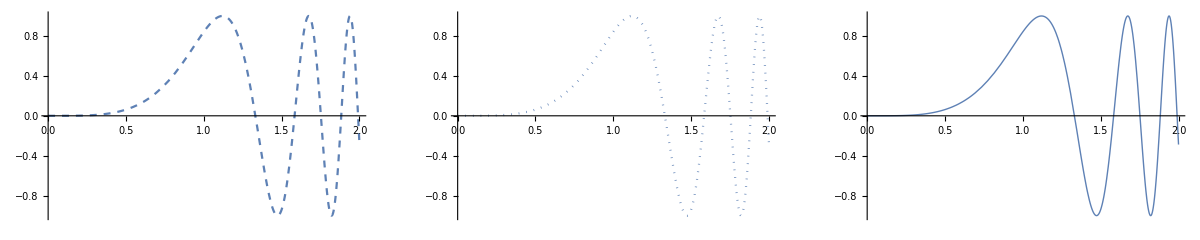

```mathematica
GraphicsRow[Plot[Sin[x^4],{x,0,2},PlotStyle->#]&/@{Dashed,Dotted,Thick}]
```

```mathematica
Text@Style[Grid[{#,"=",Expand[#]}&/@Table[(1+x)^n,{n,9}],Alignment->Left],"TranditionalForm"]
```

1+x | = | 1+x
(1+x)^2 | = | 1+2 x+x^2
(1+x)^3 | = | 1+3 x+3 x^2+x^3
(1+x)^4 | = | 1+4 x+6 x^2+4 x^3+x^4
(1+x)^5 | = | 1+5 x+10 x^2+10 x^3+5 x^4+x^5
(1+x)^6 | = | 1+6 x+15 x^2+20 x^3+15 x^4+6 x^5+x^6
(1+x)^7 | = | 1+7 x+21 x^2+35 x^3+35 x^4+21 x^5+7 x^6+x^7
(1+x)^8 | = | 1+8 x+28 x^2+56 x^3+70 x^4+56 x^5+28 x^6+8 x^7+x^8
(1+x)^9 | = | 1+9 x+36 x^2+84 x^3+126 x^4+126 x^5+84 x^6+36 x^7+9 x^8+x^9

Mathematica 6부터 Table의 반복자에 {x, list} 형태를 쓸 수 있습니다. Map, Function 조합이 하던 일을 Table로도 할 수 있게 된거죠.

```mathematica
Table[x^2,{x,{a,b,c}}]
```

{a^2,b^2,c^2}

```mathematica
GraphicsRow[Table[Plot[Sin[x^4],{x,0,2},PlotStyle->sty],{sty,{Dashed,Dotted,Thick}}]]
```

-Graphics-

이제 Sort 함수를 살펴 봅시다.

```mathematica
myList=RandomInteger[100,15]
```

{54,69,15,27,9,19,53,40,68,53,22,56,86,26,86}

```mathematica
Sort[myList]
```

{9,15,19,22,26,27,40,53,53,54,56,68,69,86,86}

Sort 명령에 임의의 정렬 방식을 부여하려면 두 개 이상의 입력을 받아서 올바른 순서일 때 True를 반환하는 함수를 정의해야 합니다.

```mathematica
Sort[myList,Function[{x,y},x>y]]
```

{86,86,69,68,56,54,53,53,40,27,26,22,19,15,9}

```mathematica
Sort[myList,Function[#1>#2]]
```

{86,86,69,68,56,54,53,53,40,27,26,22,19,15,9}

```mathematica
Sort[myList,#1>#2&]
```

{86,86,69,68,56,54,53,53,40,27,26,22,19,15,9}

한 가지 방법만 있는 건 아니죠.

```mathematica
Reverse@Sort@myList
```

{86,86,69,68,56,54,53,53,40,27,26,22,19,15,9}

```mathematica
Sort[myList,Greater]
```

{86,86,69,68,56,54,53,53,40,27,26,22,19,15,9}

하지만, 벡터의 크기로 정렬하고 싶다면, Function을 쓰는 게 가장 좋은 방법입니다.

```mathematica
myList=RandomInteger[100,{10,3}]
```

{{77,25,54},{39,23,56},{39,42,98},{87,21,43},{22,7,66},{64,95,20},{69,35,6},{88,17,67},{0,78,54},{9,12,18}}

```mathematica
Sort[myList,Norm[#1]<Norm[#2]&]
```

{{9,12,18},{22,7,66},{39,23,56},{69,35,6},{0,78,54},{77,25,54},{87,21,43},{88,17,67},{39,42,98},{64,95,20}}

```mathematica
Clear[myList]
```

### 함수형 프로그래밍

Apply 명령은 인자로 함수와 표현을 받아서 표현의 헤드를 함수로 교체하여 반환합니다.

```mathematica
Apply[Times,{a,b,c}]
```

a b c

Apply의 중위 연산자는 @@ 입니다.

```mathematica
Times@@{a,b,c}
```

a b c

시각적인 예를 하나 살펴봅시다.

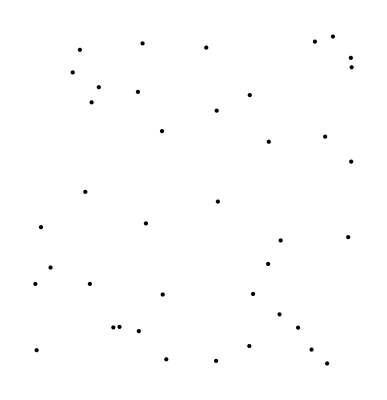

```mathematica
pts=Point@RandomReal[{-1,1},{40,2}];
Graphics@pts
```

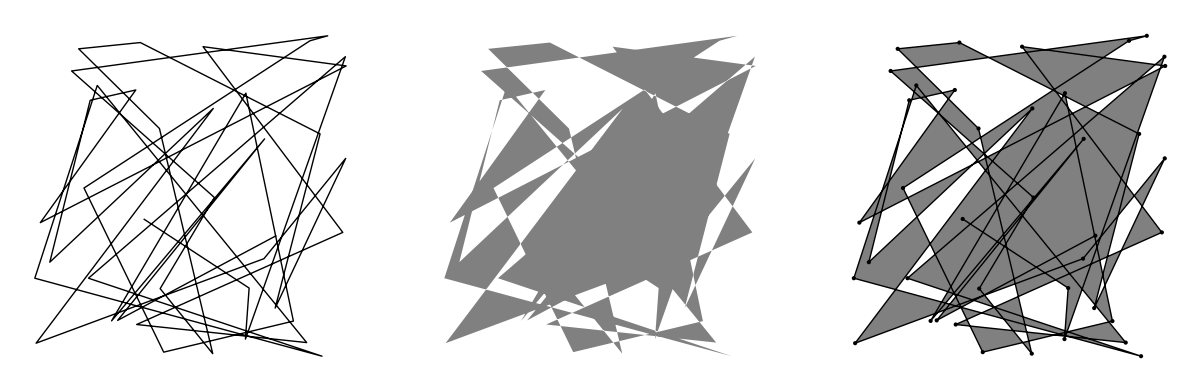

```mathematica
GraphicsRow[{Graphics[Line@@pts],Graphics[{Gray,Polygon@@pts}],Graphics[{{Gray,Polygon@@pts},Line@@pts,pts}]},Dividers->All]
```

```mathematica
Clear[pts]
```

Thread 명령은 여러 개의 리스트를 묶어서 함수에게 넘겨줍니다.

```mathematica
Thread[f[{a,b,c},{1,2,3}]]
```

{f[a,1],f[b,2],f[c,3]}

Thread를 이용하면 왼쪽 리스트의 값에서 오른쪽 리스트의 값으로 향하는 룰을 쉽게 만들 수 있습니다.

```mathematica
Thread[{a,b,c}->{1,2,3}]
```

{a→1,b→2,c→3}

Thread가 하는 역할을 잘 생각해보면, 행렬의 Transpose 대용으로 사용할 수도 있음을 알 수 있죠.

```mathematica
Thread[{{a,b,c},{1,2,3}}]
```

{{a,1},{b,2},{c,3}}

#### 카이사르의 암호

```mathematica
encode=StringReplace[#, Thread[CharacterRange["a","z"]->RotateLeft@CharacterRange["a","z"]]]&;
decode=StringReplace[#, Thread[CharacterRange["a","z"]->RotateRight@CharacterRange["a","z"]]]&;
```

```mathematica
encode=StringReplace[#1, Thread[CharacterRange["a","z"]->RotateLeft[CharacterRange["a","z"],#2]]]&;
decode=StringReplace[#1, Thread[CharacterRange["a","z"]->RotateRight[CharacterRange["a","z"],#2]]]&;
```

## 제어문과 반복문

가장 간단한 반복문은 Do 명령입니다.

```mathematica
myList={};
Do[PrependTo[myList,k],{k,10}];
myList
```

{10,9,8,7,6,5,4,3,2,1}

아래 방법이 훨씬 간단하죠.

```mathematica
Reverse@Range[10]
```

{10,9,8,7,6,5,4,3,2,1}

다음 Do 예제는 펙토리얼을 계산합니다.

```mathematica
x=1;
Do[x=k x,{k,4}];
x
```

24

이걸 이용해서 fac 함수를 정의해 봅시다.

```mathematica
fac[n_]:=(x=1;Do[x=k x,{k,n}];x)
```

```mathematica
TabView[Table[ToString[n]~~"!"->fac[n],{n,15}],13]
```

123456789101112131415

### 술어(Predicates)

논리학에서 참이나 거짓이 되는 구문을 술어(predicate)라고 합니다.

```mathematica
PrimeQ[2^16+1]
```

True

```mathematica
Table[EvenQ[n],{n,10}]
```

{False,True,False,True,False,True,False,True,False,True}

방정식 자체도 쓸모가 많은 술어가 됩니다.

```mathematica
2==3
```

False

```mathematica
N[π]==1.0π
```

True

!expr은 Not[expr]의 전위 연산자입니다.

```mathematica
!False
```

True

```mathematica
!PrimeQ[8]
```

True

Unequal의 중위 연산자는 !=입니다.

```mathematica
2≠3
```

True

Select 명령은 조건에 만족하는 원소만 골라내는 데 사용합니다.

```mathematica
Select[Range[30],PrimeQ]
```

{2,3,5,7,11,13,17,19,23,29}

4 이상인 원소만 고른다면,

```mathematica
Select[{1,2,3,4,5,6},#≥4&]
```

{4,5,6}

1부터 1000까지의 수 중에서 정수 인수가 3개가 넘는 수는,

```mathematica
Select[Range[1000],Length[FactorInteger[#]]>3&]
```

{210,330,390,420,462,510,546,570,630,660,690,714,770,780,798,840,858,870,910,924,930,966,990}

### 제어문: If, Which, Piecewise

소수 여부를 표에 나타내어 봅시다.

```mathematica
Text@Grid[Table[{k,If[PrimeQ@k,"prime","composite"]},{k,101,117,2}],Dividers->Gray]
```

101 | prime
103 | prime
105 | composite
107 | prime
109 | prime
111 | composite
113 | prime
115 | composite
117 | composite

Which 명령은 첫 번째로 True를 반환하는 술어의 다음 인자를 반환한다.

```mathematica
Text@Grid[Table[{n,Which[n==1,"is a unit",PrimeQ[n],"is a prime",EvenQ[n],"is an even composite",OddQ[n],"is an odd composite"]},{n,10}],Alignment->{{Right,Left}}]
```

1 | is a unit
2 | is a prime
3 | is a prime
4 | is an even composite
5 | is a prime
6 | is an even composite
7 | is a prime
8 | is an even composite
9 | Which[ODdQ[9],is an odd composite]
10 | is an even composite

Piecewise 명령도 비슷한 역할을 한다.

```mathematica
Text@Grid[Table[{n,Piecewise[{{"is a unit", n==1}, {"is a prime", PrimeQ[n]}, {"is an even composite", EvenQ[n]}, {"is an odd composite", OddQ[n]}}]},{n,10}],Alignment->{{Right,Left}}]
```

1 | is a unit
2 | is a prime
3 | is a prime
4 | is an even composite
5 | is a prime
6 | is an even composite
7 | is a prime
8 | is an even composite
9 | is an odd composite
10 | is an even composite

### 반복문: While, For

1000보다 큰 수 중에서 가장 작은 소수를 찾는다고 하면,

```mathematica
k=1000;
While[!PrimeQ[k],Increment[k]];
k
```

1009

같은 일을 하는 명령을 For 문으로 만들어 볼까요?

```mathematica
For[k=1000,!PrimeQ[k],k++];k
```

1009

## 유효영역: With와 Module

임의의 n 각형을 그리는 명령은 아래와 같다.

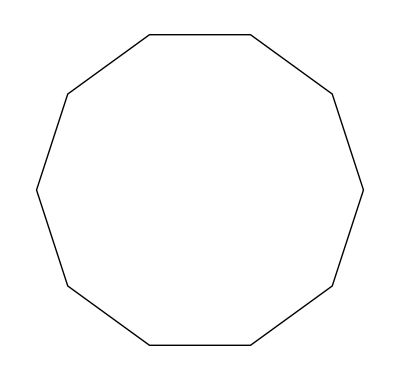

```mathematica
n=10;
Graphics@Line@Table[{Cos[t],Sin[t]},{t,0,2π,(2π)/n}]
```

위 명령을 실행하고, n에 관한 방정식을 풀으려면 문제가 발생한다.

```mathematica
Solve[3n+1==2,n]
```

Solve::ivar: 10 is not a valid variable.

Solve[False,10]

n을 지협적으로만 정의하여 사용하면 문제가 없다.

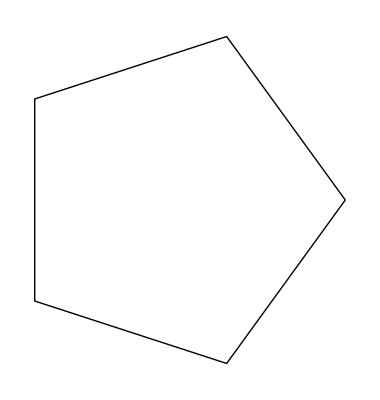

```mathematica
Clear[n];
With[{n=5},Graphics@Line@Table[{Cos[t],Sin[t]},{t,0,2π,(2π)/n}]]
```

이제는 Global` 영역에 n이 할당되지 않은 걸 알 수 있다.

```mathematica
n
```

n

지협적으로 할당한 n은 다른 부분의 계산에 영향을 미치지 않는다.

```mathematica
Solve[3n+1==2,n]
```

## 패턴

아래 정의에서 왼쪽의 x_가 패턴이다.

```mathematica
Clear[f,g,u];
f[x_]:=x+1
```

패턴은 형태만 맞으면 어떤 구조에도 적용할 수 있다.

```mathematica
f[g[u]]
```

1+g[u]

패턴에 제한을 줘서 사용하면 제어문을 대체할 수 있습니다.

```mathematica
Clear[f];
f[x_?NumericQ]:=x+1
```

```mathematica
f[24]
```

25

```mathematica
f[g[u]]
```

f[g[u]]

```mathematica
?*Q
```

#### 콜라츠의 추측(Collatz conjecture)

1937년에 처음으로 이 추측을 제기한 로타르 콜라츠의 이름을 딴 것으로 3n+1 추측, 울람 추측, 혹은 헤일스톤(우박) 수열 등 여러 이름으로 불린다. 콜라츠 추측은 임의의 자연수가 다음 조작을 거쳐 항상 1이 된다는 추측이다.

짝수라면 2로 나눈다.

홀수라면 3을 곱하고 1을 더한다.

1이면 조작을 멈추고, 1이 아니면 첫 번째 단계로 돌아간다.

```mathematica
Clear[f]
f[n_?EvenQ]:=n/2
f[n_?OddQ]:=3n+1
```

For example

```mathematica
NestWhileList[f,342,#≠1&]
```

{342,171,514,257,772,386,193,580,290,145,436,218,109,328,164,82,41,124,62,31,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

밑줄 두 개 __ (BlankSequence[])은 길이가 1 이상의 순열과 일치하는 패턴이다.

```mathematica
Clear[f,a];
f[x__Integer]:=Times[x]
```

```mathematica
f[1,2,3]
```

6

```mathematica
f[3]
```

3

```mathematica
f[1,2,a]
```

f[1,2,a]

밑줄 세 개 ___ (BlankNullSequence[])는 길이가 0 이상인 순열과 일치하는 패턴이다.

```mathematica
Clear[myPlot];
myPlot[f_,iter_List,opts___Rule]:=Plot[f,iter,opts,PlotStyle->Thick,PlotLabel->"y="~~ToString[TraditionalForm[f]],AxesLabel->{iter⟦1⟧,"y"}]
```

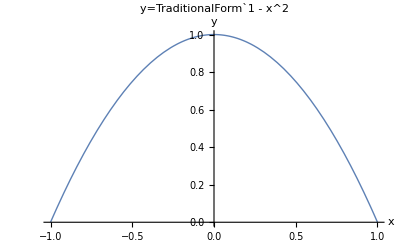

```mathematica
myPlot[1-x^2,{x,-1,1}]
```